## Lesson

Convert list of digits into an integer:

```mathematica
FromDigits[{5,6,1,7,8}]
```

56178

Reverse the digits of an integer:

```mathematica
IntegerReverse[56178]
```

87165

Do a computation, timing how long it takes

```mathematica
Timing[Table[i,{i,1000}]][[1]]
Timing[Range[1000]][[1]]
```

0.000157

6.×10^-6

## Questions

Q1. Find a simpler form for Module[{a, i}, a=0; For[i=1, i≤1000, i++, a=i*(i+1)+a];a].

```mathematica
Total[Table[i(i+1),{i,1000}]]
```

334334000

Q2. Find a simpler form for Module[{a, i}, a=x; For[i=1, i≤10, i++, a=1/(1+a)];a].

```mathematica
Nest[1/(1+#)&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

Q3. Find a simpler form for Module[{i, j, a}, a={}; For[i=1, i≤10, i++, For[j=1, j≤10, j++, a=Join[a, {i, j}]]];a].

```mathematica
Flatten[Array[List,{10,10}]]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

Q4. Make a line plot of the timing for computing n^n for n up to 1000

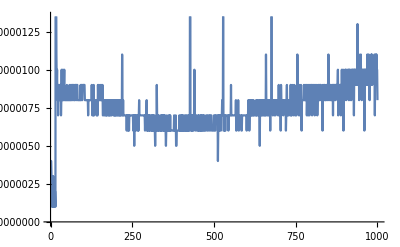

```mathematica
ListLinePlot[Timing[#^#][[1]]&/@Range[1000]]
```

Q5. Make a line plot of the timing for Sort to sort Range[n] from a random order, for n up to 200.

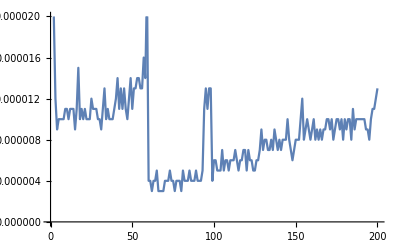

```mathematica
ListLinePlot[Timing[Sort[RandomSample[Range[#]]]][[1]]&/@Range[200]]
```